```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* constantes fisicas *)
Clear[hbar,e,massae,eps0]
hbar=1.0545718 10^-34;(* constante de Planck *)
e=1.6021766 10^-19 ;(* carga do eletron *)
massae=9.10938356 10^-31 ;(* masa do eletron *)
eps0=8.8541878176 10^-12;(* constante de permissividade do vácuo *)
```

```mathematica
Clear[deltaEc,deltaEv,me,mh,ctedielet,camadas,a]
(* os seguintes dados são para nanocristais de Perovskita *)
deltaEc=1.25e; (* altura do poco do eletron *)
deltaEv=1.45e; (* altura do poco do buraco *)
me=massae.15 ;(* massa efetiva do eletron *)
mh=massae.14 ;(* massa efetiva do buraco *)
ctedielet=4.96; (* cte dieletrica *)
camadas=18; (* numero de camadas *)
a=camadas.59 10^-9;(* espessura do nanoplatelete *)
Print[a]
```

1.062×10^-8

```mathematica
Clear[mi,eps]
(* outras constântes *)
mi=1/(1/me+1/mh); (* mu_perp *)
eps=ctedielet eps0; (* permissividade do material *)
```

```mathematica
Clear[keFunc,kappaeFunc,fTranscEFunc,EchuteE,khFunc,kappahFunc,fTranscHFunc,EchuteH]
keFunc[energia_]:=Sqrt[2me energia]/hbar(* função k do elétron *)
kappaeFunc[energia_]:=Sqrt[2me(deltaEc-energia)]/hbar(* função kappa do elétron *)
fTranscEFunc[energia_]:=keFunc[energia]Tan[keFunc[energia]a/2]-kappaeFunc[energia](* eq. transcendental do elétron *)
EchuteE[]:=(For[Ei=0,Ei<deltaEc,Ei+=deltaEc/1000,
If[fTranscEFunc[Ei]fTranscEFunc[Ei+deltaEc/1000 ]<0,Break[]]
];
Return[Ei])(* retorna um valor aproximado para o valor de energia correspondente a primeira raiz de fTranscEFunc *)
khFunc[energia_]:=Sqrt[2mh energia]/hbar(* função k do buraco *)
kappahFunc[energia_]:=Sqrt[2mh(deltaEv-energia)]/hbar(* função kappa do buraco *)
fTranscHFunc[energia_]:=khFunc[energia]Tan[khFunc[energia]a/2]-kappahFunc[energia] (* eq. transcendental do buraco *)
EchuteH[]:=(For[Ei=0,Ei<deltaEv,Ei+=deltaEv/1000,
If[fTranscHFunc[Ei]fTranscHFunc[Ei+deltaEv/1000 ]<0,Break[]]
];
Return[Ei])(* retorna um valor aproximado para o valor de energia correspondente a primeira raiz de fTranscHFunc *)
```

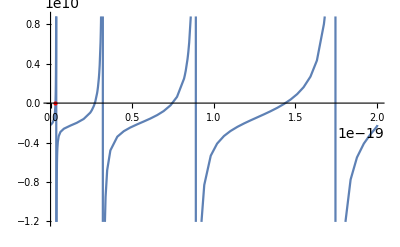

```mathematica
Clear[Ee,ke,kappae]
Ee=energia/.FindRoot[fTranscEFunc[energia],{energia,EchuteE[]}];
ke=keFunc[Ee];
kappae=kappaeFunc[Ee];

Show[Plot[fTranscEFunc[energia],{energia,0,deltaEc}],Graphics[{PointSize[Medium],Red,Point[{Ee,0}]}]]
```

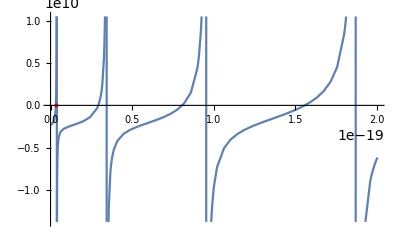

```mathematica
Clear[Eh,kh,kappah]
Eh=energia/.FindRoot[fTranscHFunc[energia],{energia,EchuteH[]}];
kh=khFunc[Eh];
kappah=kappahFunc[Eh];

Show[Plot[fTranscHFunc[energia],{energia,0,deltaEc}],Graphics[{PointSize[Medium],Red,Point[{Eh,0}]}]]
```

```mathematica
(* tamanho do infinito para a variavel a e "dobro do infinito" para x.
Esse ponto é escolhido como sendo o ponto em que a função de onda do elétron tem valor 10^-3 *)
L=2Log[Cos[ke a/2]Exp[kappae a/2]10^3]/kappae;
```

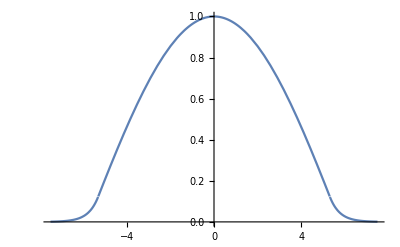

```mathematica
Clear[psie]
(* funcao de onda do elétron em função da distância x *)
psie[x_]=Piecewise[{{Cos[ke a/2]Exp[kappae a/2]Exp[kappae x],x<-a/2},{Cos[ke x],Abs[x]<a/2},{Cos[ke a/2]Exp[kappae a/2]Exp[-kappae x],x>a/2}}];
Plot[psie[x],{x,-L/2,L/2}]
```

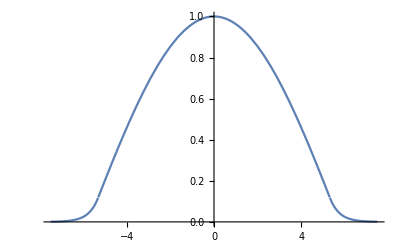

```mathematica
Clear[psih]
(* funcao de onda do buraco em função da distância x *)
psih[x_]=Piecewise[{{Cos[kh a/2]Exp[kappah a/2]Exp[kappah x],x<-a/2},{Cos[kh x],Abs[x]<a/2},{Cos[kh a/2]Exp[kappah a/2]Exp[-kappah x],x>a/2}}];
Plot[psih[x],{x,-L/2,L/2}]
```

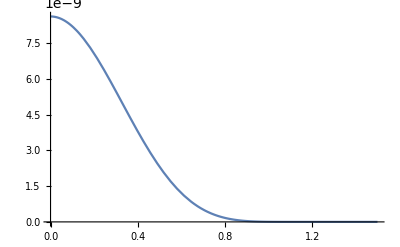

```mathematica
Clear[pInte,pAux,p]
pInte[z_,a_]:=(psie[z+a]psih[z])^2+(psie[z]psih[z+a])^2
pAux[a_]:=NIntegrate[pInte[z,a],{z,-L/2,L/2-a}]
p=Interpolation[Table[{a,pAux[a]},{a,0,L,L/100}]];
Plot[p[a],{a,0,L},PlotRange->All]
```

```mathematica
Clear[F,GInte,G,J13,J24Inte,J24,J,KInte,Kk]
(* F(a) *)
F[a_]:=2Pi(lamb Sqrt[1-beta^2]a/2+lamb^2/4)Exp[-2Sqrt[1-beta^2]a/lamb]

(* G(a) *)
GInte[w_,a_]:=2Pi(1-w^2)/w/(1+w^2)(a(1-beta^2)/lamb)^2Exp[-Sqrt[1-beta^2]a/lamb(1/w+w)]
G[a_]:=NIntegrate[GInte[w,a],{w,0,1}]

(* J(a) *)
J13[a_]:=2Pi(Sqrt[1-beta^2]a/2/lamb-1/4)Exp[-2*Sqrt[1-beta^2]a/lamb]
J24Inte[w_,a_]:=Pi a Sqrt[1-beta^2](1/w^2-1)(-4/lamb/(w+1/w)^2-2a Sqrt[1-beta^2]/(w+1/w)/lamb^2)Exp[-a Sqrt[1-beta^2]/lamb(w+1/w)]
J24[a_]:=NIntegrate[J24Inte[w,a],{w,0,1}]
J[a_]:=J13[a]+J24[a]

(* K(a) *)
KInte[w_,a_]:=a Pi beta(1/w^2-1)Exp[-a beta/lamb(1/w-w)]
Kk[a_]:=NIntegrate[KInte[w,a],{w,0,(1-Sqrt[1-beta^2])/beta}]
```

```mathematica
Clear[d,aux,A,B,c,EsAux,Es]
(* o ponto de mínimo é procurado em um range de lambda entre [lambIni, lambFin] com lambN pontos e um range de beta entre [betaIni, betaFin] com betaN pontos *)
lambIni=3. 10^-9;
lambFin=4. 10^-9;
lambN=5;
betaIni=.6;
betaFin=1.;
betaN=5;
Es={};(* array das energias calculadas para cada valor de beta e lamb *)
Timing[
For[beta=betaIni,beta<=betaFin,beta+=(betaFin-betaIni)/(betaN-1),
EsAux={};
For[lamb=lambIni,lamb<=lambFin,lamb+=(lambFin-lambIni)/(lambN-1),
d=NIntegrate[p[a]F[a],{a,0,L}];
aux=NIntegrate[p[a]G[a],{a,0,L}];
A=Ee d+hbar^2/2/me aux;
B=Eh d+hbar^2/2/mh aux;
c=-hbar^2/2/mi NIntegrate[p[a]J[a],{a,0,L}]-e^2/4/Pi/eps NIntegrate[p[a]Kk[a],{a,0,L}];
Eb=((A+B+c)/d-Ee-Eh)/e/10^-3;
AppendTo[EsAux,Eb]
];
AppendTo[Es,EsAux];
Print[EsAux]
]
][[1]]/60
valores={a 10^9,lambIni 10^9,lambFin 10^9,lambN,betaIni,betaFin,betaN};
out={valores};
For[i=1,i≤lambN,i++,AppendTo[out,Es[[i]]]]
nome="nanoplatelete_"<>ToString[a 10^9]<>".csv";
Export[nome,out];(* exporta um arquivo .csv do array "valores" na primeira linha e o array "Es" nas demais linhas *)
```

NIntegrate::inumr: The integrand (2.85955×10^17 a^2 ⅇ^(-2.66667×10^8 a (1/w+w)) (1-w^2))/(w (1+w^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{-53.8552,-55.0226,-55.507,-55.5314,-55.243}

{-54.0147,-55.1349,-55.593,-55.6036,-55.3091}

{-53.488,-54.6731,-55.1964,-55.2685,-55.0302}

{-51.1814,-52.7458,-53.5844,-53.919,-53.8996}

{-38.3259,-42.5197,-45.358,-47.2372,-48.427}

18.2492